## Numerical results for trophical transmission model with multiple infections

```mathematica
SetDirectory[NotebookDirectory[]]
<<Tools`
ParallelNeeds["Tools`"](* Import package Tools that define useful functions*)
```

/Users/phuongnguyen/Work/multipleinfections/code

# ODEs

```mathematica
dIsdt = R[Iw, Is, Iww]- d Is- Πs[Ds, Dw, Dww] Is  - ηw  Is ;
dIwdt =  (1-p)ηw Is  - (d + αw)Iw - Πw[Ds, Dw,Dww, βw]Iw; 
dIwwdt =  p ηw Is  - (d + αww)Iww - Πww[Ds, Dw, Dww,βww]Iww; 
dDsdt =B[Ds, Dw,Dww, Is, Iw, Iww]  - μ Ds - (λww + λw) Ds;
dDwdt =(λw + 2(1-q)λww) Ds- (μ + σw) Dw - (2(1-q)λww +λw)Dw;
dDwwdt = q λww Ds + (2(1-q)λww + λw)Dw - (μ + σww)Dww;
dWdt = fw Dw +fww Dww- δ W - ηw Is;

forceInf = {ηw -> γ W, λw -> βw Iw, λww -> βww Iww};
odesRes = {dIsdt, dIwdt, dIwwdt, dDsdt, dDwdt, dDwwdt, dWdt};
varRes = {Is, Iw, Iww, Ds, Dw, Dww, W};
vartRes = {Is[t], Iw[t], Iww[t], Ds[t], Dw[t], Dww[t], W[t]};
```

# Graph format and parallel computation

```mathematica
includeFrame = True(*{{True, False}, {True,False}}*);
imageSize = 600;
frameStyle = Directive[Black,Thickness[0.003]];
labelStyle = {Black, FontSize-> 14};
ColorData[97,"ColorList"]
colorlist = {%[[7]], %[[8]], %[[-2]] }
hostcolors=ColorData[97,"ColorList"]⟦{1,5,7}⟧
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

{RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.736782672705901, 0.358, 0.5030266573755369]}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.363898, 0.618501, 0.782349]}

# Linear birth function for intermediate host

```mathematica
func0 = {R[Iw, Is, Iww] -> r(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  βw(Ds + Dw+Dww),Πww[Ds, Dw,Dww, βww]->  βww(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};
sysfunc0 = odesRes/.forceInf/.func0;
sysNDSolvefunc0 = MakeSystem[varRes, t,sysfunc0];
```

## Jacobian matrix

```mathematica
Jmatfunc0 = D[sysfunc0, {varRes}];
```

## Ecological trajectories

```mathematica
prEco0 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 0.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 6.5,fww-> 7.5, δ-> 0.9};

maxt = 50;

init0= {Is[0]== 4, Iw[0] == 2,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 10};

sols0 = NSolve[Thread[(odesRes/.func0/.forceInf/.prEco0) == 0], varRes];
ndsol0 = NDSolve[Join[sysNDSolvefunc0/.prEco0, init0], varRes, {t, 0, maxt}] ;

p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, 25}, All}, PlotLegends->{"I_s",  "D_s"}, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->imageSize,Frame->True,FrameStyle->frameStyle,LabelStyle->labelStyle,PlotStyle->hostcolors];

p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, 25}, All},PlotLegends->{"I_w", "I_ww", "D_w", "D_ww", "W"}, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->imageSize, Frame-> True,FrameStyle->frameStyle,LabelStyle->labelStyle,PlotStyle->{Directive[Darker[Blue],Full],Directive[Darker[Blue],Dashed],Directive[Darker[Green],Full],Directive[Darker[Green],Dashed],Darker[Red]}];
Grid[{{p1, p2}}]
(*Export["diseasefree_linear.jpg",%]*)
```

```mathematica
tabtopl=Table[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsol0]⟦1⟧, {t, 0, maxt,0.01}];
```

```mathematica
ListLinePlot[Transpose[tabtopl],PlotRange->All,MultiaxisArrangement->{{1,2,3,4},5}]
```

-Graphics-

## Bifurcation γ

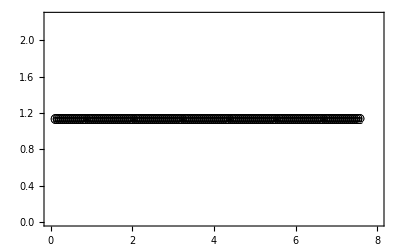

```mathematica
parγ = {ρ -> 1.2, d -> 0.1,r -> 2.5, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 1.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 1.1};
γrange = Range[0.1, 8, 0.05];

solsγ = NSolve[Thread[(odesRes/.func0/.forceInf/.parγ/.γ-> 0.1) == 0], varRes];
eqinit = {Is->1.1309523809523814,Iw->0,Iww->0,Ds->2.0000000000000004,Dw->0,Dww->0,W->0};

eqγzero = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, eqinit];
{#}& /@Transpose[{γrange, Is/.eqγzero}];
p0 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parγ, γ, γrange, eqγzero], PlotStyle-> Black, Frame->includeFrame, FrameLabel->{"Pool to intermediate host transmission (γ)", "Equilibrium"}, PlotLegends->{"I_s"}];
{#}& /@Transpose[{γrange, Ds/.eqγzero}];
p1 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parγ, γ, γrange, eqγzero], PlotStyle-> Gray, PlotLegends->{"D_s"}];
Show[p0, p1]
```

## Bifurcation β_w

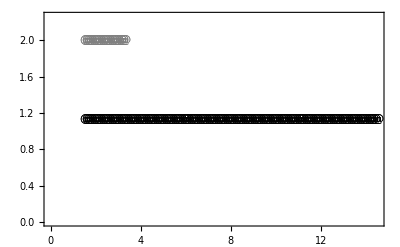

```mathematica
parβw = {ρ -> 1.2, d -> 0.1,r -> 2.5, γ -> 3.5, αw-> 0, αww-> 0,  βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 1.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 1.1, Κ-> 100};
βwrange = Range[1.5, 14.5, 0.1];

solsβw = NSolve[Thread[(sysfunc0/.parβw/.βw-> 1.5) == 0], varRes];

eqinit = {Is->1.1309523809523812,Iw->0,Iww->0,Ds->2.0000000000000004,Dw->0,Dww->0,W->0};

eqβwzero = FollowRoot[sysfunc0, parβw, βw, βwrange, varRes, eqinit];
{#}& /@Transpose[{βwrange, Is/.eqβwzero}];
p0 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parβw, βw, βwrange, eqβwzero], PlotStyle-> Black, Frame->includeFrame, FrameLabel->{"Intermediate - definitive hosts transmission β_w", "Equilibrium"}, PlotLegends->{"I_s"}];
{#}& /@Transpose[{βwrange, Ds/.eqβwzero}];
p1 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parβw, βw, βwrange, eqβwzero], PlotStyle-> Gray, PlotLegends->{"D_s"}];
Show[p0, p1]
```

# Nonlinear birth function for intermediate host

```mathematica
func1 = {R[Iw, Is, Iww] -> r(1-k(Is + Iw+Iww))(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  (ρ +βw)(Ds + Dw+ Dww),Πww[Ds, Dw, Dww, βww]->  (ρ+βww)(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};

sysfunc1 = odesRes/.forceInf/.func1;
sysNDSolvefunc1 = MakeSystem[varRes, t, sysfunc1];
```

## Jacobian matrix

```mathematica
Jmatfunc1 = D[sysfunc1, {varRes}];
```

## Ecological trajectories

## Disease free equilibrium

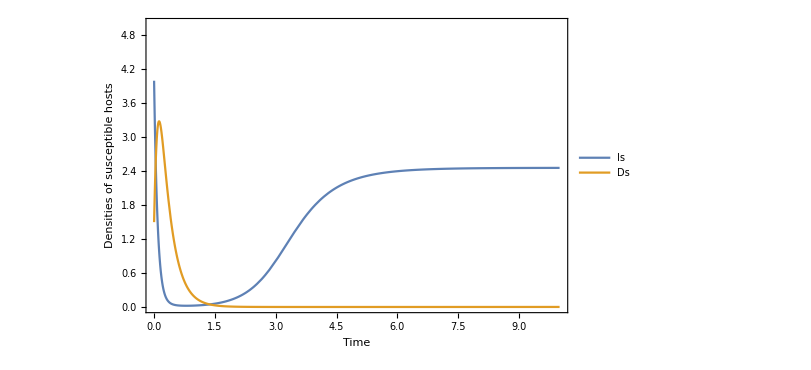
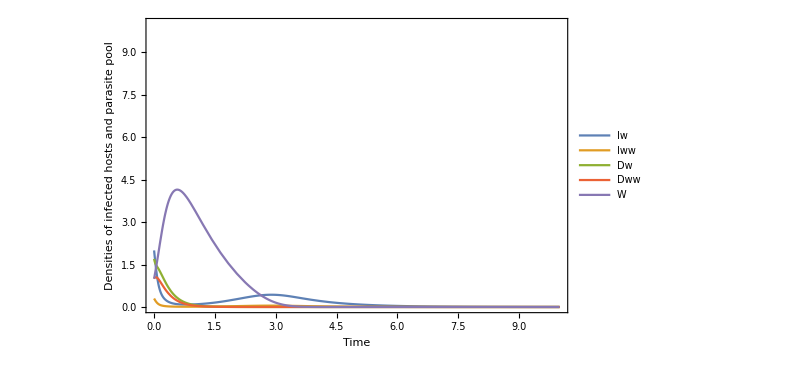
-Graphics- | -Graphics-

```mathematica
prEcoNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 0.9, k -> 0.26};

maxt = 10;

solsNL = NSolve[Thread[(sysfunc1/.prEcoNL) == 0], varRes];

{Is[0]== 4, Iw[0] == 2,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 1};
ndsolNL = NDSolve[Join[sysNDSolvefunc1/.prEcoNL, %], varRes, {t, 0, maxt}] ;

p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsolNL], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 5}}, PlotLegends->{"Is",  "Ds"},Frame->includeFrame,FrameStyle->frameStyle, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->imageSize];

p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsolNL], {t, 0, maxt}, PlotRange->{{0, maxt},{0, 10}},PlotLegends->{"Iw", "Iww", "Dw", "Dww", "W"}, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->imageSize];
Grid[{{p1, p2}}]
(*Export["Diseasefree.jpeg",%]*)
```

## Disease stable equilibrium

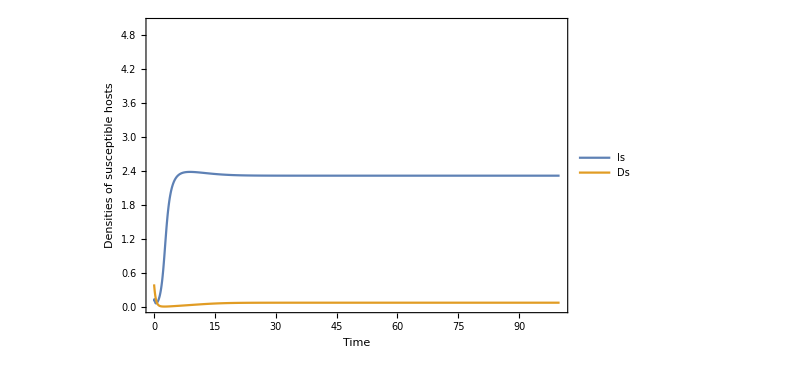
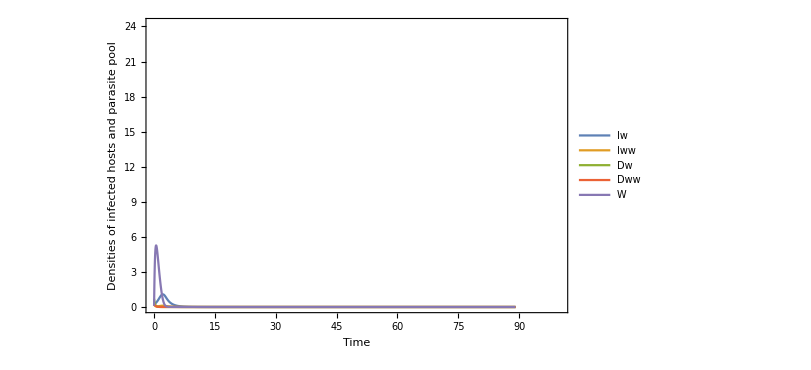
-Graphics- | -Graphics-

```mathematica
prEcoDSNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, α-> 0, βw-> 0.5, βww-> 4.5,p-> 0.1, c-> 1.4, μ-> 3.9, σ-> 0,q-> 0.01, fw -> 36, fww-> 36,δ-> 0.9, k -> 0.26};



condsimplifyNL = {αw-> α, αww-> α, σw-> σ, σww-> σ};

maxt = 100;

(*{Is[0]== 1.6, Iw[0] == 1.2,Iww[0]==0.32, Ds[0] ==3.4, Dw[0] == 1.7,Dww[0]==1.1, W[0] == 3.1};*)
{Is[0]== 0.1, Iw[0] == 0.2,Iww[0]==0.32, Ds[0] ==0.4, Dw[0] == 0.7,Dww[0]==0.1, W[0] == 0.1};
ndsolDS = NDSolve[Join[sysNDSolvefunc1/.condsimplifyNL/.prEcoDSNL, %], varRes, {t, 0, maxt}] ;

solsDS = NSolve[Thread[(sysfunc1/.condsimplifyNL/.prEcoDSNL) == 0], varRes, Reals,  WorkingPrecision->15];

p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsolDS], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 5}}, PlotLegends->{"Is",  "Ds"},Frame-> includeFrame, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->imageSize];
p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsolDS], {t, 0, maxt}, PlotRange->{{0, maxt},{0, 24.2}},PlotLegends->{"Iw", "Iww", "Dw", "Dww", "W"}, Frame-> includeFrame, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->imageSize];
Grid[{{p1, p2}}]
```

## Bifurcation f_w (f_ww = ϵ f_w) parameter set 1

## Parameter set 1

CALCULATE

```mathematica
parfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 2};
fwstart = 29;
fwend = 40.5;
fwstep = 0.2;
fwrange = Range[29, 40.5, 0.2];

(*Find all solutions of the system with the given parameter values*)
solsfwAll = NSolve[Thread[(odesRes/.func1/.forceInf/.fww-> ϵ fw/.parfw/.fw-> 36) == 0], varRes, Reals];

(*Select disease circulation solutions*)
fwAllPositive= ParallelTable[NSolvePositive[sysfunc1/.fww-> ϵ fw, parfw, fw -> i, varRes, eq], {i, fwstart, fwend, fwstep}];
(*Select disease free solutions*)
solsfwzero = Select[solsfwAll, (Is/.#)> 0 &&(Iw/.#)== 0 &&(Iww/.#)== 0&&(Ds/.#)>0 &&(Dw/.#)== 0 &&(Dww/.#)== 0 &&(W/.#)== 0 &][[1]];
```

PLOT

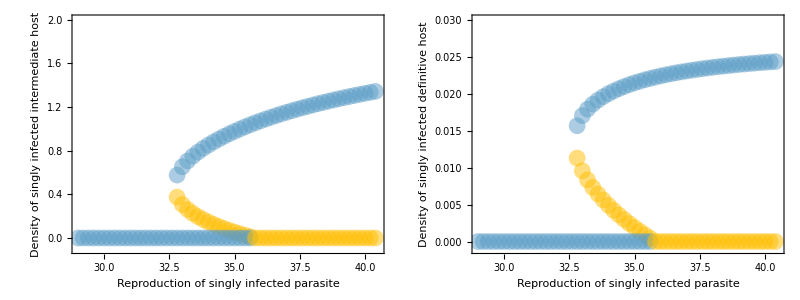

```mathematica
fwlist = fw/.Flatten[fwAllPositive, 1];
eqfwlist = eq/.Flatten[fwAllPositive, 1];

rangeIw = {{fwstart, fwend}, {-0.1, 2}};
rangeDw = {{fwstart, fwend}, {-0.001, 0.03}};

Iwfwlist = Iw/.eqfwlist;
MakeListPlotData[fwlist, Iwfwlist];
p0 = ListPlot[%, PlotStyle->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwlist, eqfwlist, colorlist, True],  PlotRange -> rangeIw, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Reproduction of singly infected parasite", "Density of singly infected intermediate host"},LabelStyle->labelStyle,FrameStyle->frameStyle];

Dwfwlist = Dw/.eqfwlist;
MakeListPlotData[fwlist, Dwfwlist];
p1 = ListPlot[%, PlotStyle->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwlist, eqfwlist, colorlist, True], PlotRange->rangeDw, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Reproduction of singly infected parasite", "Density of singly infected definitive host"},LabelStyle->labelStyle,FrameStyle->frameStyle];


eqfwzero = ConstantArray[solsfwzero, Length[fwrange]];
MakeListPlotData[fwrange, Iw/.eqfwzero];
p2 = ListPlot[%, PlotStyle->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero, colorlist, True], PlotRange->rangeIw, ImageSize->imageSize,LabelStyle->labelStyle,FrameStyle->frameStyle];

MakeListPlotData[fwrange, Dw/.eqfwzero];
p3 = ListPlot[%, PlotStyle->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero, colorlist, True], PlotRange->rangeDw, ImageSize->imageSize,LabelStyle->labelStyle,FrameStyle->frameStyle];

pp0 = Show[p0,  p2];
pp1 = Show[p1, p3];

Grid[{{pp0, pp1}}]
(*Export["bistability.jpg",%]*)
```

## Parameter set 2

CALCULATION

```mathematica
parfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 1};
fwrangeFWrd = Range[40.5, 51.5, 0.5];
fwrangeBWrd = Range[40.5, 32, -0.5];
fwrange = Range[32, 51.5, 0.3];

(*Find all solutions of the system with the given parameter values*)
solsfwAll = NSolve[Thread[(odesRes/.func1/.forceInf/.fww-> ϵ fw/.parfw/.fw-> 40.5) == 0], varRes, Reals];

(*Select disease circulation solutions*)
solsfw= Select[solsfwAll, (Is/.#)> 0 &&(Iw/.#)> 0 &&(Iww/.#)> 0 &&(W/.#)> 0 &][[1]];

(*Select disease free solutions*)
solsfwzero = Select[solsfwAll, (Is/.#)> 0 &&(Iw/.#)== 0 &&(Iww/.#)== 0&&(Ds/.#)>0 &&(Dw/.#)== 0 &&(Dww/.#)== 0 &&(W/.#)== 0 &][[1]];

eqfwFWrd = FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, fwrangeFWrd, varRes, solsfw];
eqfwBWrd = FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, fwrangeBWrd, varRes, solsfw];

rangeIs = {{fwrangeBWrd[[-1]], fwrangeFWrd[[-1]]}, {-0.1, 2}};
rangeDs = {{fwrangeBWrd[[-1]], fwrangeFWrd[[-1]]}, {-0.01, 0.03}};
```

FindRoot::reged: The point {2.30006,0.0176722,0.00196358,0.0760433,0.000630176,-1.69407×10^-21,0.00295133} is at the edge of the search region {0.,∞} in coordinate 6 and the computed search direction points outside the region.

PLOTTING

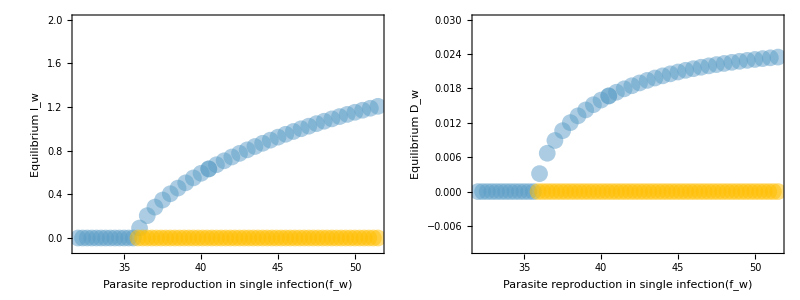

```mathematica
xaxis =fwrangeFWrd[[1;; Length[eqfwFWrd]]];
MakeListPlotData[xaxis, Iw/.eqfwFWrd];
p0 = ListPlot[%, PlotStyle->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwFWrd, colorlist, True], PlotRange->rangeIs, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Parasite reproduction in single infection(f_w)", "Equilibrium I_w"},LabelStyle->labelStyle,FrameStyle->frameStyle];

MakeListPlotData[xaxis, Dw/.eqfwFWrd];
p1 = ListPlot[%, PlotStyle->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwFWrd, colorlist, True], PlotRange->rangeDs, ImageSize->imageSize, Frame->includeFrame, FrameLabel->{"Parasite reproduction in single infection(f_w)", "Equilibrium D_w"},LabelStyle->labelStyle,FrameStyle->frameStyle];

xaxis = fwrangeBWrd[[1;;Length[eqfwBWrd]]];
MakeListPlotData[xaxis, Iw/.eqfwBWrd];
p2 = ListPlot[%, PlotStyle->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwBWrd, colorlist, True], PlotRange->rangeIs, ImageSize->imageSize,LabelStyle->labelStyle,FrameStyle->frameStyle];

MakeListPlotData[xaxis, Dw/.eqfwBWrd];
p3 = ListPlot[%, PlotStyle->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwBWrd, colorlist, True], PlotRange->rangeDs, ImageSize->imageSize,LabelStyle->labelStyle,FrameStyle->frameStyle];


eqfwzero = ConstantArray[solsfwzero, Length[fwrange]];
MakeListPlotData[fwrange, Iw/.eqfwzero];
p4 = ListPlot[%, PlotStyle->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero, colorlist, True], PlotRange->rangeIs, ImageSize->imageSize,LabelStyle->labelStyle,FrameStyle->frameStyle];

MakeListPlotData[fwrange, Dw/.eqfwzero];
p5 = ListPlot[%, PlotStyle->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero, colorlist, True], PlotRange->rangeDs, ImageSize->imageSize,LabelStyle->labelStyle,FrameStyle->frameStyle];

ppp0 = Show[p0,  p2, p4];
ppp1 = Show[p1, p3, p5];

Grid[{{ppp0, ppp1}}]
(*Export["bifurcation_fw_NL.jpg", %]*)
```

```mathematica
On[Assert];
rr= Range[35, 37, 0.02];
FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, rr, varRes, solsfwzero];
xx =ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, rr, %];
pos = Position[xx, "*", 1, 1][[1]][[1]];
xx[[pos]] == "*"//Assert
xx[[pos-1]] == "." //Assert
fwbifur = rr[[pos]]
```

35.84

## Bifurcation ϵ and f_w (f_ww = ϵ f_w)

CALCULATE

```mathematica
parϵfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26};

ϵstart = 0;
ϵend = 6;
ϵinterval = 0.2;
fwstart = 29;
fwend = 40;
fwinterval = 0.8;

ϵfwAllresults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parϵfw, {ϵ -> i}, {fw-> j}, ϵfw, eq,varRes],{i, ϵstart, ϵend, ϵinterval}, {j, fwstart, fwend, fwinterval}];
```

PLOT

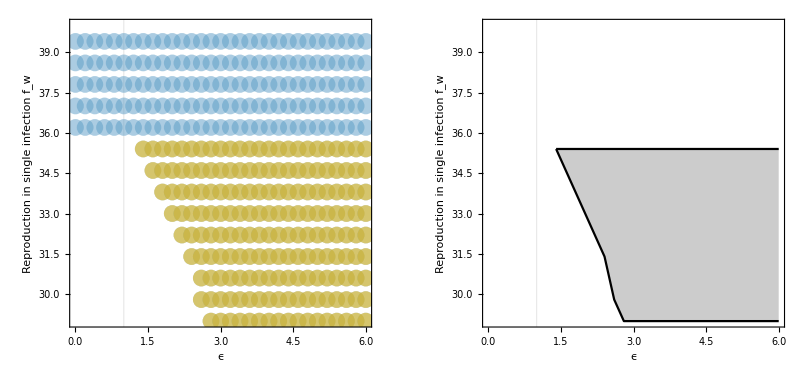

```mathematica
eqϵfw =eq/. Flatten[ϵfwAllresults, 2];
ϵfwlist = ϵfw/.Flatten[ϵfwAllresults, 2];
rangeϵfw= {{ϵstart , ϵend}, {fwstart , fwend}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parϵfw,{ϵ, fw}, ϵfwlist, eqϵfw, colorlist, True];
MakeListPlotData[ϵfwlist[[All, 1]], ϵfwlist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->rangeϵfw, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"ϵ", "Reproduction in single infection f_w"}, GridLines->{{1},{}}, GridLinesStyle-> {Thick,Black}, LabelStyle->labelStyle,FrameStyle->frameStyle,AspectRatio->1];
GetBoundaryLine[ϵfwlist];
p1 =ListLinePlot[%, AspectRatio->1, PlotRange->rangeϵfw, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"ϵ", "Reproduction in single infection f_w"}, LabelStyle->labelStyle,GridLines->{{1},{}}, GridLinesStyle-> {Thick,Black}, PlotStyle-> Black, Filling-> {1-> {2}}];
GraphicsGrid[{{p0, p1}}]
```

## Bifurcation of single and double infection (β_w and β_ww) setting f_ww=ϵ f_w

## Parameter set 1 (f_ww=f_w)

CALCULATE

```mathematica
parmanip = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 1, fw -> 36};

βwstart = 0;
βwend = 4;
βwstep = 0.2;
βwwstart = 0;
βwwend = 20;
βwwstep = 1;

manipAllResults1 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanip, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

PLOT

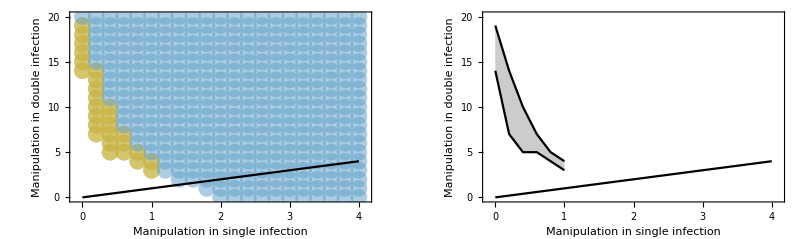

```mathematica
parmanip = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 1, fw -> 36};

equilibrium =eq/. Flatten[manipAllResults1 , 2];
parslist = β/.Flatten[manipAllResults1, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanip,{βw, βww}, parslist, equilibrium, colorlist, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black];
pp2 = Show[{p0, p1}];
GetBoundaryLine[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, PlotStyle-> Black, Filling-> {1-> {2}}];
l2 = Show[{lp1, p1}];
GraphicsGrid[{{pp2, l2}}]
```

## Parameter set 2 (f_ww = 2 f_w)

CALCULATE

```mathematica
parmanip = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 2, fw -> 35};

βwstart = 0;
βwend = 4;
βwstep = 0.2;
βwwstart = 0;
βwwend = 20;
βwwstep = 1;

manipAllResults2 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanip, {βw -> x}, {βww-> y}, β, eq,varRes],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

PLOT

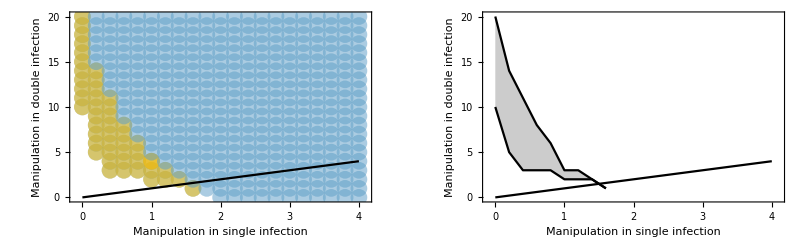

```mathematica
parmanip = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 2, fw -> 35};

equilibrium =eq/. Flatten[manipAllResults2 , 2];
parslist = β/.Flatten[manipAllResults2, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanip,{βw, βww}, parslist, equilibrium, colorlist, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"},  LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black];
pp2 = Show[{p0, p1}];
GetBoundaryLine[parslist];
lp2 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, PlotStyle-> Black, Filling-> {1-> {2}}];
l2 = Show[{lp2, p1}];
GraphicsGrid[{{pp2, l2}}]
```

## Parameter set 3 (f_ww = 0.5 f_w)

CALCULATE

```mathematica
parmanip = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 0.5, fw -> 36};

βwstart = 0;
βwend = 4;
βwstep = 0.2;
βwwstart = 0;
βwwend = 20;
βwwstep = 1;

manipAllResults3 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanip, {βw -> x}, {βww-> y}, β, eq,varRes, 14],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.5469854076984010904. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.85931842463833474. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.8593720341698733517. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.6821067282658343367. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

PLOT

{{{0.,17},{0.2,10},{0.4,7},{0.6,6},{0.8,5},{1.,4},{1.2,3}},{{0.,19},{0.2,14},{0.4,10},{0.6,7},{0.8,5},{1.,4},{1.2,3}}}

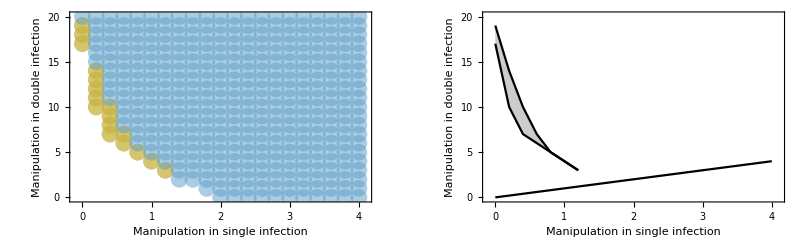

```mathematica
parmanip = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 0.5, fw -> 36};

equilibrium =eq/. Flatten[manipAllResults3 , 2];
parslist = β/.Flatten[manipAllResults3, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanip,{βw, βww}, parslist, equilibrium, colorlist, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"},  LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black];
GetBoundaryLine[parslist]
lp3 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, PlotStyle-> Black, Filling-> {1-> {2}}];
l2 = Show[{lp3, p1}];
GraphicsGrid[{{p0, l2}}]
```